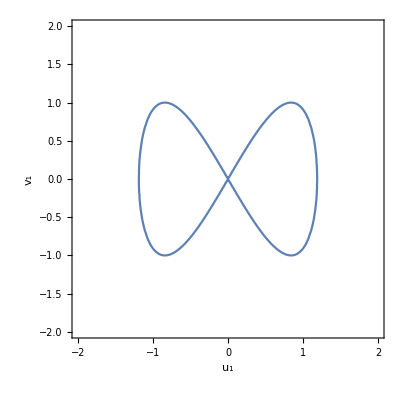

```mathematica
ContourPlot[2^(3/2)Subscript[u, 1]^2-2 Subscript[u, 1]^4-Subscript[v, 1]^2==0, {Subscript[u, 1], -2, 2}, {Subscript[v, 1], -2, 2},FrameLabel->{"u_1", "v_1"}]
```

```mathematica
ParametricPlot3D[{{Subscript[u, 1], Subscript[u, 1]^2-2^(1/2), 2^(1/2)Subscript[u, 1] Sqrt[2^(1/2)-Subscript[u, 1]^2]},{Subscript[u, 1], Subscript[u, 1]^2-2^(1/2), -2^(1/2)Subscript[u, 1] Sqrt[2^(1/2)-Subscript[u, 1]^2]}},{Subscript[u, 1],-2^(1/4), 2^(1/4)}, Axes->True,AxesOrigin->{0,0,0},Boxed->False,PlotStyle->{Blue, Blue}]
```

-Graphics3D-

```mathematica
2^(1/4)//N
```

1.18921

(√2 u1 | -2+√2 u1^2 | 0
-2+√2 u1^2 | √2 u1 | -1
0 | 0 | 0)

{0,2+√2 u1-√2 u1^2,-2+√2 u1+√2 u1^2}

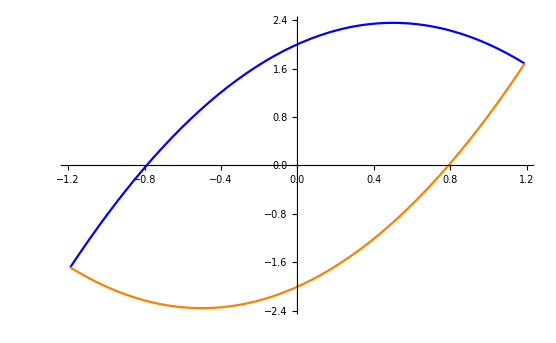

```mathematica
vectorField[u1_,u2_,v2_] := {{-1 + 2^(-1/2)u1^2+2^(-1/2)u2^2},{-v2 +2^(1/2)u1 u2},{0}};
vectorField[u1, u2, v2];
{{r1}, {r2}, {r3}} = D[vectorField[u1, u2, v2], {{u1,u2,v2}}];
jac = {r1, r2, r3}/.{u2->u1^2-2^(1/2), v2->-2^(1/2)u1 Sqrt[2^(1/2)-u1^2]}//Simplify;
jac//MatrixForm
eigs = Eigenvalues[jac]//Simplify
eigs2 =eigs[[2;;3]]; (* don't plot the zero eigenvalue *)
Plot[eigs2, {u1, -2^(1/4),2^(1/4)},PlotStyle->{Blue, Orange}]
```

```mathematica
Solve[2+√2 u1-√2 u1^2==0,u1]
```

{{u1→-(-√2-√(2 (1+4 √2)))/(2 √2)},{u1→-(-√2+√(2 (1+4 √2)))/(2 √2)}}